# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
OrganizeWFDataMultTau[fileName_]:=Module[{axesLabel,d,numTaus,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
numTaus=Length[i⟦1⟧]-1;
Return[{axesLabel,d,numTaus}];
](* OrganizeWFDataMultTau Module *)
```

#### DataToPlotFormat[data_]

This function takes a data file and organizes it such that for each Ilk value, there is an independent xValue column corresponding to the yValue column

As output, this function returns a single data member which is organized as a list of sublists.  Each sublist corresponds to a different τ value and is comprised by a list of x,y coordinates that can be used to plot the data.

```mathematica
DataToPlotFormat[data_]:=Module[{organizedData},
organizedData=Transpose[data];
organizedData=Select[Transpose[{organizedData⟦1⟧,#}],NumberQ[#⟦2⟧]&]&/@organizedData⟦2;;⟧;
Return[organizedData];
](* DataToPlotFormat Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
iInVal=ToExpression[Flatten[StringCases[fileName,"LPFWaveform_iin_"~~iIn:NumberString~~"_tau_sweep.txt"->iIn]]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements

File Name: LPFWaveform_iin_3.00_tau_sweep.txt

## Information Processing (Run-time)

### Process Waveform data from input file

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBounds ={0.5001,1.5};
AbsoluteTiming[{axesLabel,data,numTaus}=OrganizeWFDataMultTau[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
timeFilteredData=Select[data,#⟦1⟧>timeBounds⟦1⟧&];
timeFilteredData=Select[timeFilteredData,#⟦1⟧<=timeBounds⟦2⟧&];
timeFilteredData=DataToPlotFormat[timeFilteredData];(*Organize data to allow it to be plottable*)
d=DataToPlotFormat[data];(*Organize data to allow it to be plottable*)
(* Extract tau values and labels from imported dataset *)
tauLabels=Rest[axesLabel];
tauVals=ToExpression[Flatten[StringCases[tauLabels,"i(vmeas_im):tau_"~~tau:NumberString~~"`"-> tau]]];
(* Take only positive current values as valid data *)
validTimeFilteredData=Select[#,#⟦2⟧>0&]&/@timeFilteredData;
(* Clear timeFilteredData from memory *)
Remove[timeFilteredData];
(* Extract x-values from dataset *)
xValsExp=Transpose[#]⟦1⟧&/@validTimeFilteredData;
```

```mathematica
xValsExp
```

{{0.50012,0.500139,0.50016,0.500181,0.500207,0.500237,0.500273,0.500318,0.500376,0.500435,0.500495,0.500556,0.500621,0.500692,0.50077,0.500855,0.500951,0.501056,0.501175,0.501307,0.501457,0.501627,0.501821,0.502047,0.502311,0.502628,0.503017,0.503506,0.50414,0.504956,0.505724,0.506539,0.507507,0.50781,0.508053,0.508824,0.509473,0.510283,0.511142,0.512127,0.513289,0.514736,0.516581,0.518974,0.521965,0.525524,0.529649,0.534411,0.539926,0.546348,0.553854,0.562656,0.573024,0.58532,0.600061,0.618022,0.640448,0.669482,0.709179,0.768494,0.843494,0.918494,0.993494,1.06849,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500113,0.500161,0.500203,0.500242,0.500281,0.500322,0.500366,0.500417,0.500479,0.500554,0.500646,0.500767,0.500883,0.501003,0.501126,0.501258,0.501402,0.501559,0.501733,0.501927,0.502142,0.502383,0.502654,0.502959,0.503306,0.503704,0.504166,0.504711,0.505365,0.50617,0.50719,0.508522,0.510065,0.511576,0.513226,0.515438,0.51735,0.518936,0.52051,0.522147,0.52405,0.526409,0.529519,0.533642,0.538924,0.545242,0.552576,0.561057,0.570944,0.582608,0.596543,0.613452,0.634421,0.661278,0.697386,0.749752,0.824752,0.899752,0.974752,1.04975,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.50025,0.500371,0.500479,0.500579,0.500675,0.500777,0.500885,0.501008,0.501154,0.501334,0.501552,0.501833,0.502132,0.502427,0.502735,0.50306,0.503412,0.503797,0.504223,0.504696,0.505222,0.50581,0.506469,0.507211,0.508052,0.509014,0.510125,0.511426,0.512979,0.514878,0.517271,0.520406,0.523995,0.527596,0.531693,0.533171,0.534354,0.538137,0.541259,0.544885,0.548697,0.552949,0.557999,0.564139,0.572032,0.582273,0.595274,0.611181,0.630484,0.654394,0.685309,0.728021,0.793544,0.868544,0.943544,1.01854,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500375,0.500616,0.500849,0.501062,0.501256,0.501452,0.501663,0.501892,0.502161,0.502488,0.502885,0.503381,0.504037,0.504616,0.505232,0.505866,0.506548,0.507292,0.508113,0.509022,0.510032,0.511158,0.512418,0.513831,0.515425,0.517236,0.519311,0.521718,0.524555,0.527973,0.532223,0.537766,0.544456,0.55135,0.559907,0.563224,0.571768,0.57803,0.585248,0.59275,0.601601,0.612077,0.625415,0.642564,0.664567,0.692619,0.729364,0.780874,0.855874,0.930874,1.00587,1.08087,1.1,1.1306,1.2056,1.2806,1.3556,1.4306,1.5},{0.500128,0.500409,0.500775,0.50114,0.501467,0.501767,0.502058,0.50237,0.502699,0.503077,0.503527,0.504081,0.504758,0.505631,0.506525,0.507421,0.508357,0.509346,0.51042,0.511598,0.5129,0.514344,0.51595,0.517741,0.519743,0.521992,0.52453,0.527415,0.530724,0.534571,0.539127,0.544683,0.55181,0.56155,0.571615,0.585323,0.589165,0.601459,0.610474,0.621328,0.633114,0.646453,0.662555,0.682295,0.707062,0.738668,0.780671,0.840933,0.915933,0.990933,1.06593,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500409,0.500901,0.501388,0.50184,0.502249,0.502638,0.503051,0.503478,0.503964,0.504535,0.505241,0.506092,0.507175,0.508413,0.509592,0.510835,0.512133,0.513536,0.515071,0.516764,0.518639,0.520721,0.523039,0.525626,0.52852,0.531771,0.535444,0.539625,0.544436,0.550067,0.556855,0.565538,0.578394,0.592071,0.606409,0.621469,0.635383,0.649356,0.663984,0.680825,0.699915,0.723204,0.75183,0.78836,0.837322,0.908989,0.983989,1.05899,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500409,0.501025,0.501634,0.502217,0.502735,0.503231,0.503728,0.504271,0.504864,0.505563,0.506424,0.507458,0.508763,0.510359,0.511828,0.513383,0.514997,0.516737,0.518636,0.520729,0.523046,0.525616,0.528473,0.531654,0.535204,0.539176,0.54364,0.548687,0.554448,0.561139,0.569177,0.57964,0.595678,0.61015,0.624507,0.639606,0.656891,0.674126,0.69248,0.71244,0.734839,0.76114,0.79323,0.834224,0.889597,0.964597,1.0396,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5}}

### Plot Data

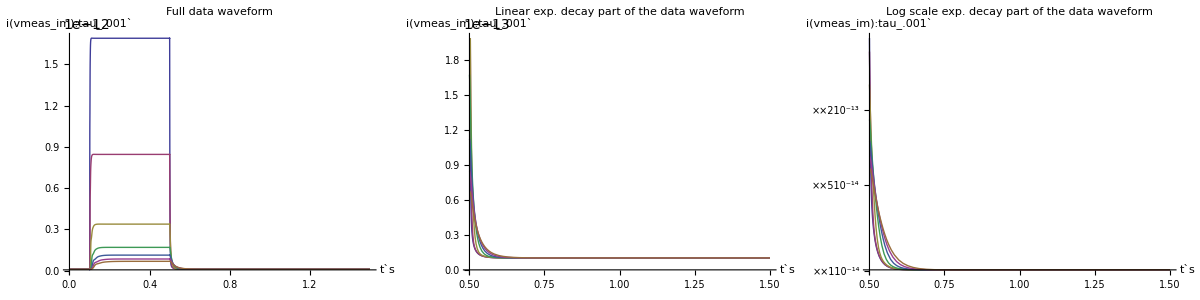
Data Waveforms
-Graphics-

```mathematica
imgSize=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[timeFilteredData,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Linear exp. decay part of the data waveform",Bold]],
ListLogPlot[timeFilteredData,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize, PlotLabel->Style["Log scale exp. decay part of the data waveform",Bold]]}
}]}
}]
```

### Manipulate Data

#### Calculate τ using exponential fit including offset

```mathematica
imgSize=500;
workPrec=Automatic;
Manipulate[
(*plotNum=Sequence@@Flatten[Position[tauLabels,plotID]];*)
plotNum=Sequence@@Flatten[Position[tauVals,plotID]];
(* Select exponential range of data *)
selDataExp=Select[#,#⟦1⟧>lowerBoundExp&]&/@validTimeFilteredData;
selDataExp=Select[#,#⟦1⟧<upperBoundExp&]&/@selDataExp;
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
selDataExp=Transpose[{#⟦;;,1⟧-lowerBoundExp,#⟦;;,2⟧}]&/@selDataExp;
(* Find the best fit *)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[selDataExp⟦plotNum⟧,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
fooCurve=NonlinearModelFit [selDataExp⟦plotNum⟧,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
fooCurveParamsAllTau=FindFit[#,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000]&/@selDataExp;
fooCurveAllTau=Function[t,Evaluate[model/.fooCurveParamsAllTau]];
currVals={a,o,τexp}/.fooCurveParams;
errTau=Abs[currVals⟦3⟧-tauVals⟦plotNum⟧];percErrTau=(errTau/tauVals⟦plotNum⟧)*100;
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],Row[{Style["Curve Equation:  ",FontFamily->"Helvetica", Bold] ,Style[Normal[fooCurve],Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦3⟧,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}],},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]},
(*{Row[{Style["Plot ID:  ",FontFamily->"Helvetica", Bold] ,Style[plotID,Italic]}],Row[{Style["Plot Number:  ",FontFamily->"Helvetica", Bold] ,Style[plotNum,Italic]}]},*)
{
(*Show[
(*Plot[fooCurveAllTau[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],*)
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotStyle->Directive[Red,Thick],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
],*)
Show[ListPlot[selDataExp⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Darker[Red],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
]
},(*Middle Row of Grid*)
{
Show[
ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[d⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All},PlotStyle->Directive[Red,Thick]]
]
(*Heat Plot of errors for each tau value*)
}(*Bottom Row of Grid*)
}],
(*{{plotID,tauLabels⟦4⟧,"Plot ID"},tauLabels},*)
{{plotID,tauVals⟦1⟧,"Theoretical τ Value"},tauVals},
{{lowerBoundExp,xValsExp⟦plotNum⟧⟦10⟧,"Lower Bound"},Take[xValsExp⟦plotNum⟧,Min[40,Length[xValsExp⟦plotNum⟧]]],Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦plotNum⟧⟦Floor[Length[Most[xValsExp⟦plotNum⟧]]/2]⟧,"Upper Bound"},Most[xValsExp⟦plotNum⟧]},LabelStyle->Medium, 
UnsavedVariables->{model,fooCurveParams, fooCurve,currVals,errTau,selDataExp,plotNum},
TrackedSymbols->{plotID,lowerBoundExp,upperBoundExp}
]
```

FindFit::sdprec: Line search unable to find a sufficient decrease in the function value with TraditionalForm`MachinePrecision digit precision.

```mathematica
MemoryInUse[]
```

47866624

### Data Analysis

#### Accuracy of Tau Values as measured from the Manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawData=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.2781, .2892, .2856, .288, .2593, .198, .1511}, {0.5, .0055, .0036, .0162, .0023, .0021, .0022, .0012}, {0.75, .0005, .0037, .0002, .0002, .00003, .0026, .0044}, {1.00, .0007, .0001, .0021, .00003, .0017, .0032, .0031}, {1.25, .0021, .0008, .0006, .0002, .0012, .0002, .0012}, {3, .0001, .0020, .0008, .00005, .0004, .0011, .0004}});
percErrTauVals=Rest[percErrTauRawData⟦1⟧];
percErriinVals=Rest[Transpose[percErrTauRawData]⟦1⟧];
percErrPlotVals=Transpose[Rest[Transpose[Rest[percErrTauRawData]]]]
MatrixPlot[percErrPlotVals,PlotRange->{0,0.3},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

(0.2781 | 0.2892 | 0.2856 | 0.288 | 0.2593 | 0.198 | 0.1511
0.0055 | 0.0036 | 0.0162 | 0.0023 | 0.0021 | 0.0022 | 0.0012
0.0005 | 0.0037 | 0.0002 | 0.0002 | 0.00003 | 0.0026 | 0.0044
0.0007 | 0.0001 | 0.0021 | 0.00003 | 0.0017 | 0.0032 | 0.0031
0.0021 | 0.0008 | 0.0006 | 0.0002 | 0.0012 | 0.0002 | 0.0012
0.0001 | 0.002 | 0.0008 | 0.00005 | 0.0004 | 0.0011 | 0.0004)

-Graphics-

## Appendix

### Calculate τ using linear fit of log of exponential decay (old method of doing this)

```mathematica
Manipulate[
dataBounds={lowerBound,upperBound};
selData=Select[timeFilteredData-offsetMin,#⟦2⟧>0&];
xVals=Transpose[selData]⟦1⟧;
logSelectedData=Transpose[{selData⟦;;,1⟧,Log[selData⟦;;,2⟧]}];
logSelData=Select[logSelectedData,#⟦1⟧>dataBounds⟦1⟧&];
logSelData=Select[logSelData,#⟦1⟧<dataBounds⟦2⟧&];
fooLine=Fit[logSelData,{1,t},t];
barLine=FindFit[logSelData,m t+b,{m,b},t];
τ=-1/m/.barLine;
Grid[{
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isat,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMin,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Show[ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selData,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooLine,{t,0,0.7}]
]}
}],
{{lowerBound,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[xVals]/2]⟧,"Upper Bound"},xVals,Appearance->{"Labeled","Open"}}
]
```

### Playing with Exponents

#### Exponential without offset

0.1

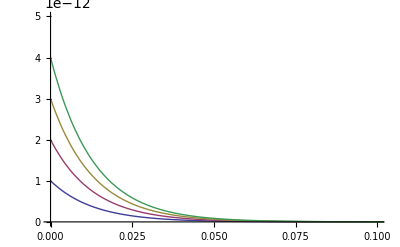

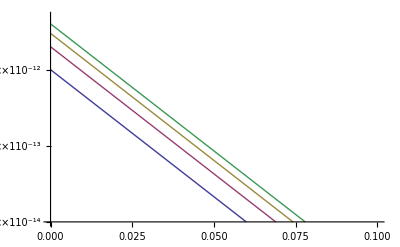

```mathematica
foo[a_,τtest_,t_]:=a*ⅇ^(-t/τtest);
a=100*10^-14;
τtest=0.013;
xMax=.1
Plot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5 a}}]
LogPlot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{a/100,5 a}}]
```

#### Exponential with offset

0.05

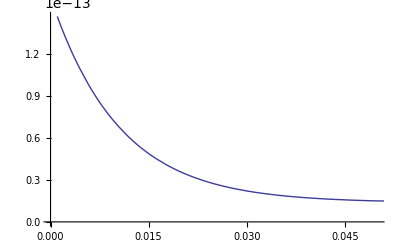

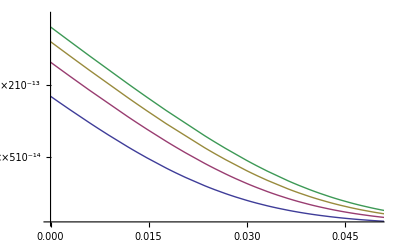

```mathematica
fooOff[a_,τtest_,t_,offset_]:=a*ⅇ^(-t/τtest)+offset;
atest=1.46548*10^-13;
τtest=0.0104876;
offsettest=1.36989*10^-14;
xMax=0.05
Plot[{fooOff[1 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,atest}}]
(*Plot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5atest}}]*)
LogPlot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{atest/10,5atest}}]
```